```mathematica
<<TopoTB`
```

#### Hamiltonian

```mathematica
H={{(kx^2+ky^2)/(2m),I α(kx-I ky)},{-I α(kx+I ky),(kx^2+ky^2)/(2m)}};
H//TraditionalForm
```

((kx^2+ky^2)/(2 m) | ⅈ α (kx-ⅈ ky)
-ⅈ α (kx+ⅈ ky) | (kx^2+ky^2)/(2 m))

#### Electronic structure calculation

```mathematica
Clear[h]
h[{kx_,ky_,kz_},m_:1,α_:0.8]=H;
lat={{1,0,0},{0,1,0},{0,0,1}};
k1={-1,0,0};k2={1,0,0};
klabel={"k1","k2"};
ds=HSPBand[h,lat,{{k1,k2,40}},klabel,0]
```

```mathematica
Clear[h]
h[{kx_,ky_,kz_},m_:1,α_:0.8]=H;
lat={{1,0,0},{0,1,0},{0,0,1}};
ds=HCalc2D[h,lat,{1,2},{10,10},{1,1},2,1,0]
```

```mathematica
Normal[ds[4]]
```

-Graphics3D-

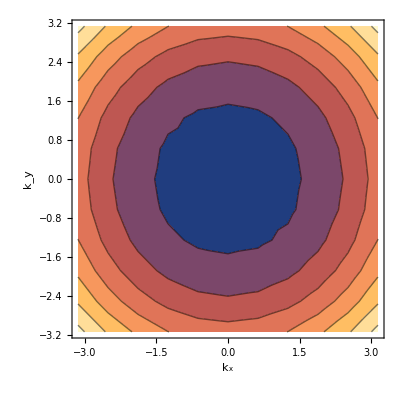
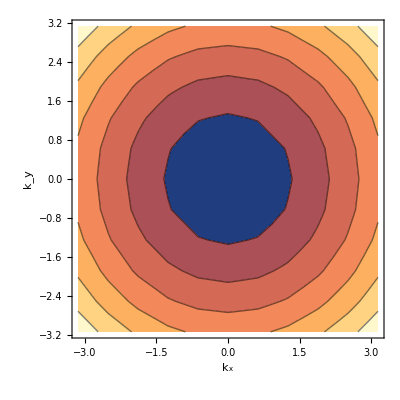

```mathematica
Normal[ds[5]]
```

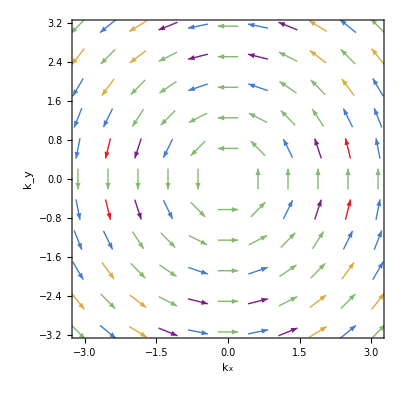
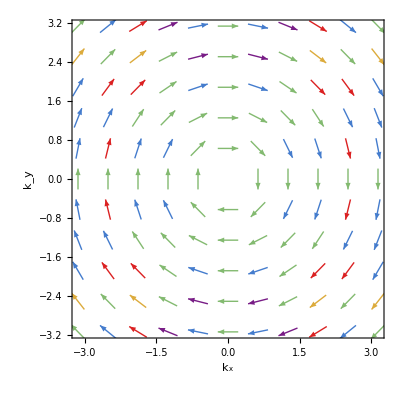

```mathematica
Normal[ds[6]]
```